```mathematica
(*single[L_,d_]:=Binomial[L/2,d/2]/2^(L/2);
combined[L_,d_]:=(2^(L/2-1)Binomial[L/2,d/2]+Binomial[L,d])/2^L;
ratio[L_,d_]:=single[L,d]/combined[L,d];
L=100;*)
```

```mathematica
single[L_,d_]:=Binomial[L/2,L*d/2]/2^(L/2);
combined[L_,d_]:=(2^(L/2-1)Binomial[L/2,L*d/2]+Binomial[L,L*d])/2^L;
ratio[L_,d_]:=single[L,d]/combined[L,d];
```

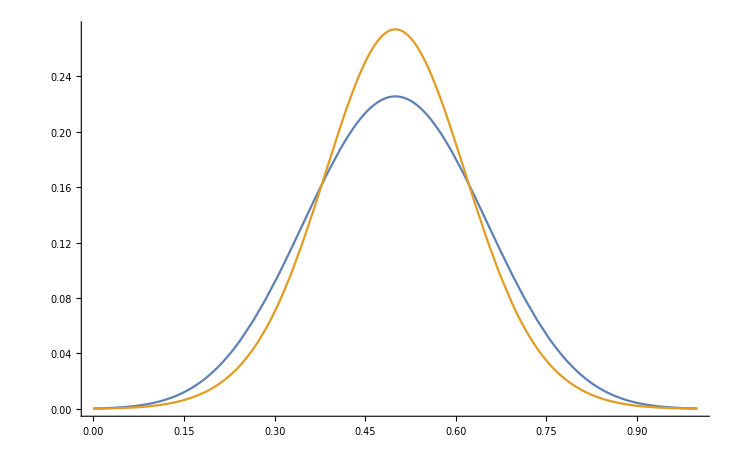

```mathematica
Plot[{single[24,d],combined[24,d]},{d,0,1},PlotRange->All]
```

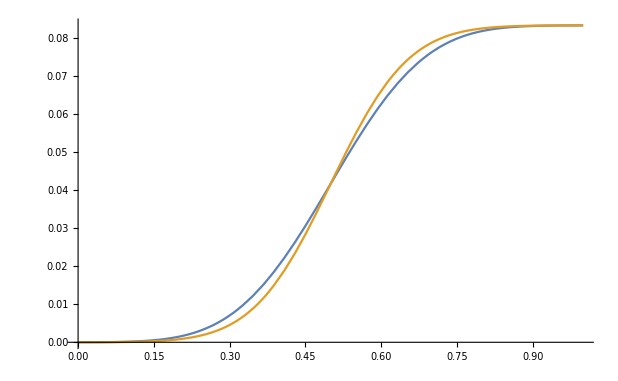

```mathematica
secdf[x_]:= Integrate[single[24,d],{d,0,x}]
cecdf[x_]:= Integrate[combined[24,d],{d,0,x}]
Plot[{ secdf[x], cecdf[x]},{x,0,1}]
```

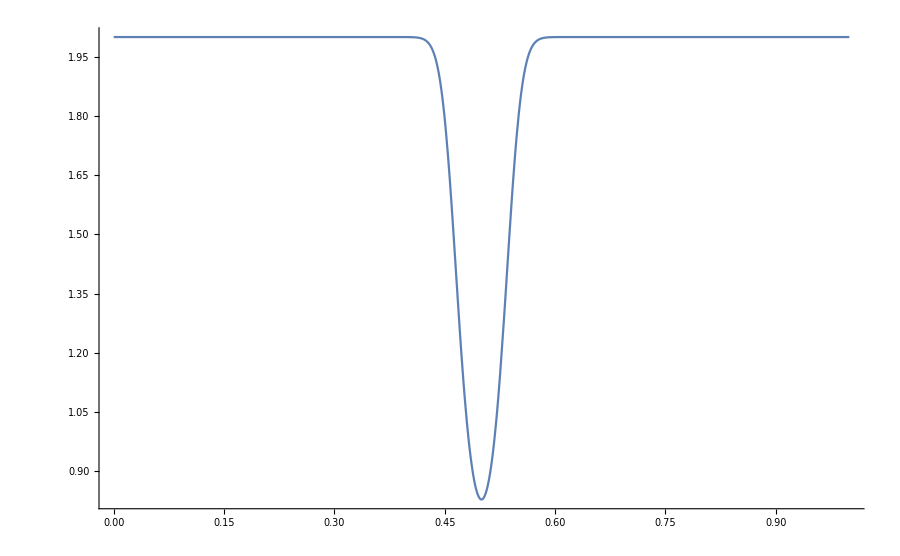

```mathematica
(*DiscretePlot[ratio[L,L*d],{d,0,1}]*)
L=1000;
Plot[ratio[L,d],{d,0,1},PlotRange->All]
(*DiscretePlot[{single[L,d], combined[L,d]},{d,0,L}]*)
```

```mathematica
Table[i,{i,0,1,0.01}]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

```mathematica
Clear[L];
inflimit=Table[Limit[ratio[L,d],L-> Infinity],{d,0.4999995,0.5000005,0.0000001}]
```

{2.,2.,0.828427,0.828427,0.828427,0.828427,0.828427,0.828427,0.828427,2.,2.}

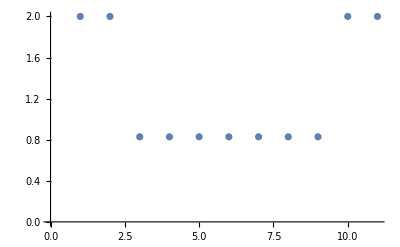

```mathematica
ListPlot[inflimit]
```

```mathematica
Limit[2^(1-L/2) Binomial[L,L/2]/Binomial[L/2,L/4 ],L-> Infinity]
```

√2

```mathematica
Clear[L];
Assuming[0<d<1,Limit[ratio[L,d],L-> Infinity]]
```

lim_(L→∞) (2^(L/2) Binomial[L/2,(d L)/2])/(2^(-1+L/2) Binomial[L/2,(d L)/2]+Binomial[L,d L])

```mathematica
Limit[ratio[L,1/2],L-> Infinity]
```

2 (-1+√2)

```mathematica
Limit[2^(1-L/2) Binomial[L,L*d]/Binomial[L/2,(L*d)/2],L-> Infinity]
```

lim_(L→∞) (2^(1-L/2) Binomial[L,d L])/Binomial[L/2,(d L)/2]

```mathematica
Limit[2^(1-L/2) Binomial[L,L*L/2]/Binomial[L/2,(L*L)/4],L-> Infinity]
```

0

```mathematica
Clear[L];
Limit[ratio[L,L/2+100],L-> Infinity]
```

2 (-1+√2)

```mathematica
N[2/(1+Sqrt[2])]
```

0.828427

```mathematica
ratio[L,d]
```

(2^(L/2) Binomial[L/2,d/2])/(2^(-1+L/2) Binomial[L/2,d/2]+Binomial[L,d])

```mathematica
Limit[2^(1-L/2) Binomial[L,d]/Binomial[L/2,d/2],L-> Infinity]
```

0

## Using Derived expressions of the Stirling approximation results for the ratio

```mathematica
stir$approx[L_,d_]:= √2 d^((-L d)/2) (1-d)^(-L/2 (1-d)) 2^(-L/2);
```

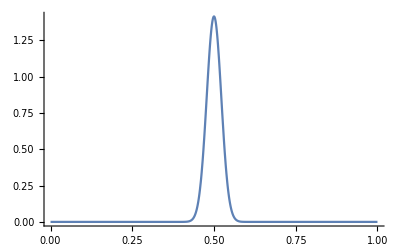

```mathematica
L=1000;
Plot[rat[L,d],{d,0,1},PlotRange->All]
```

```mathematica
Clear[L];
Assuming[0<d<1,Limit[rat[L,d],L-> Infinity]]
```

ConditionalExpression[0,d Log[1-d]<Log[2-2 d]+d Log[d]]

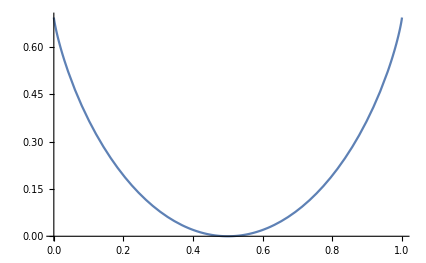

```mathematica
Plot[Log[2-2 d]+d Log[d]-(d Log[1-d]),{d,0,1}]
```

```mathematica
Limit[rat[L,1/2],L-> Infinity]
```

√2

### Plotting χ

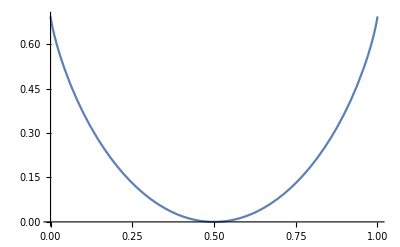

```mathematica
Plot[d Log[d]+(1-d) Log[1-d]+Log[2],{d,0,1}]
```

```mathematica
Solve[d Log[d]+(1-d) Log[1-d]+Log[2]==0,d]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Log[2]+(1-d) Log[1-d]+d Log[d]==0,d]

### Converting the Binomials to Normal Distributions in the large L limit

In the large L limit, a reasonable approximation to B[n,p] is Ν[np,np(1-p)] where N is the normal distribution.

```mathematica
Gauss[μ_,σ_,x_]:= 1/(Sqrt[2π] σ)Exp[(-(x-μ)^2)/(2 σ^2)];
```

```mathematica
(*single[L_,d_]:=Binomial[L/2,L*d/2]/2^(L/2);*)
single$norm[L_,d_,x_]:= Gauss[(L/2)*(L*d/2),  (L/2)*(L*d/2)*(1-(L*d/2)),x]/2^(L/2);
(*combined[L_,d_]:=(2^(L/2-1)Binomial[L/2,L*d/2]+Binomial[L,L*d])/2^L;*)
combined$norm[L_,d_]:=(2^(L/2-1) Gauss[(L/2)*(L*d/2),  (L/2)*(L*d/2)*(1-(L*d/2)),x]+Gauss[L*L*d,L*L*d*(1-L*d),x])/2^L;
ratio$norm[L_,d_]:=single$norm[L,d]/combined$norm[L,d];
```

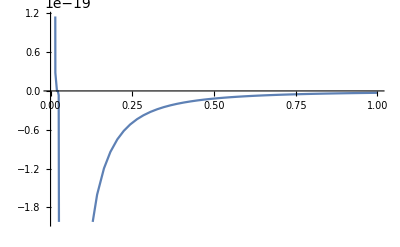

```mathematica
Plot[single$norm[100,d,d],{d,0,1}]
```